### All Data

```mathematica
$Version
```

12.3.0 for Mac OS X x86 (64-bit) (May 10, 2021)

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
allFiles=FileNames["*.csv","sample data"];
allData=Import[#,"Data"]&/@allFiles;
(*locate the folder name that includes .asc files *)
```

```mathematica
allData2=Table[i,{i,1,Length[allData]}];
For[i=1,i<=Length[allData],
allData2[[i]]=Drop[allData[[i]],4];
i++]
Dimensions[allData2]
Dimensions[allData2[[1]]]
allData2[[1]]//MatrixForm;
```

{2,128,128}

{128,128}

```mathematica
IR1100=allData2[[1]];
IR1400=allData2[[2]];
Dimensions[IR1100]
IR1100//MatrixForm;
```

{128,128}

```mathematica
IRratio14001100=Table[0,{i,1,Length[allData2[[1]]]},{j,1,Length[allData2[[1]]]}];
```

```mathematica
For[i=1,i<=Length[IR1400],
For[j=1,j<=Length[IR1400],
IRratio14001100[[i,j]]=IR1400[[i,j]]/IR1100[[i,j]];
j++];
i++]
```

### Imaging

```mathematica
Lx=20;(*um*)
Ly=20;(*um*)
nx=Length[IR1400];
ny=Length[IR1400];
d=5;
```

```mathematica
{0,0},{128,20}
```

```mathematica
Round[nx/d,1]
```

26

```mathematica
Table[-d*i,{i,0,nx}];
Table[-d*i,{i,0,ny}];
tick={{0,0},{32,5},{64,10},{96,15},{128,20}}
Table[{Round[nx/d,1],i},{i,1,Lx}];
If[nx>=ny,imgSize=500,imgSize=300];
If[nx>=ny,legSize=220,legSize=440];
```

{{0,0},{32,5},{64,10},{96,15},{128,20}}

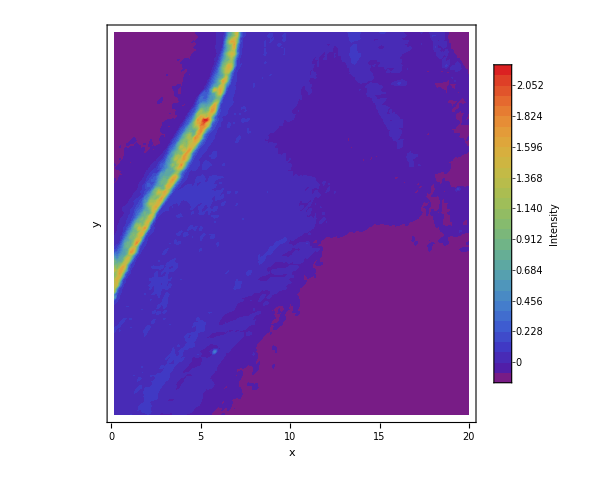
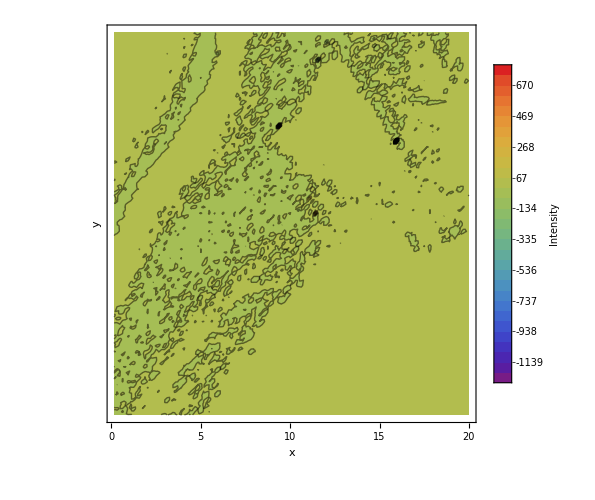
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListContourPlot[Reverse[IR1100],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->None,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]],
ListContourPlot[Reverse[IR1400],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->None,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]],
ListContourPlot[Reverse[IRratio14001100],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->Line,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]]
}
```

### Further1 (lifted and normalized by initial input intensity)

```mathematica
Io1100=73.321;
Io1400=47;
```

```mathematica
IR1100n=(IR1100-Min[IR1100]+0.00001)/Io1100;
IR1400n=(IR1400-Min[IR1400]+0.00001)/Io1400;
```

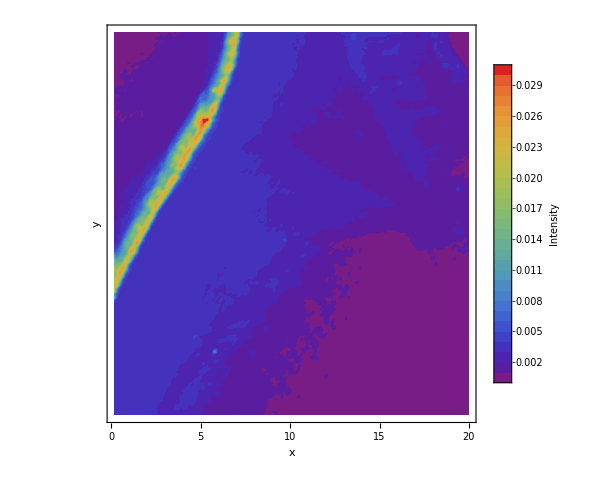
{-Graphics-,-Graphics-}

```mathematica
{ListContourPlot[Reverse[IR1100],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->None,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]],
ListContourPlot[Reverse[IR1100n],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->None,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]]
}
```

```mathematica
{ListContourPlot[Reverse[IR1100n],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->None,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]],
ListContourPlot[Reverse[IR1400n],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->None,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]]
}
```

{-Graphics-,-Graphics-}

### Ratio

```mathematica
IRratio114001100n=Table[0,{i,1,Length[allData2[[1]]]},{j,1,Length[allData2[[1]]]}];
```

```mathematica
For[i=1,i<=Length[IR1400n],
For[j=1,j<=Length[IR1400n],
IRratio114001100n[[i,j]]=IR1400n[[i,j]]/IR1100n[[i,j]];
j++];
i++]
```

### comparison

```mathematica
{ListContourPlot[Reverse[IRratio14001100],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->Line,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]],
ListContourPlot[Reverse[IRratio114001100n],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->None,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]]
}
```

{-Graphics-,-Graphics-}

```mathematica
IRratio114001100n//MatrixForm;
Max[IRratio114001100n]
Position[IRratio114001100n,Max[IRratio114001100n]]
```

1819.92

{{126,119}}

```mathematica
IRratio114001100n2=IRratio114001100n;
IRratio114001100n2[[126,119]]=0;
```

```mathematica
{ListContourPlot[Reverse[IRratio114001100n],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->Line,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]],
ListContourPlot[Reverse[IRratio114001100n2],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->None,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]]
}
```

{-Graphics-,-Graphics-}

```mathematica
For[i=1,i<=Length[IRratio114001100n2],
For[j=1,j<=Length[IRratio114001100n2],
If[IRratio114001100n2[[i,j]]>3,IRratio114001100n2[[i,j]]=0];
j++];
i++]
```

```mathematica
{ListContourPlot[Reverse[IRratio114001100n],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->Line,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]],
ListContourPlot[Reverse[IRratio114001100n2],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->True,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]],
}
```

{-Graphics-,-Graphics-,Null}

### Further2 (lift the normalized ones more0)

```mathematica
IR1100nn=IR1100n+1;
IR1400nn=IR1400n+1;
```

```mathematica
IRratio14001100nn=Table[0,{i,1,Length[allData2[[1]]]},{j,1,Length[allData2[[1]]]}];
```

```mathematica
For[i=1,i<=Length[IR1400nn],
For[j=1,j<=Length[IR1400nn],
IRratio14001100nn[[i,j]]=IR1400nn[[i,j]]/IR1100nn[[i,j]];
j++];
i++]
```

```mathematica
{ListContourPlot[Reverse[IRratio14001100],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->Line,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]],
ListContourPlot[Reverse[IRratio14001100nn],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{None,tick},{tick,None}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->30
,ContourStyle->None,GridLines->{Range[50,0,d],Range[-300,0,d]},Method->{"GridLinesInFront"->True},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}]]
}
```

{-Graphics-,-Graphics-}